```mathematica
ClearAll["Global`*"];eq=Hold[D[f[x,t],{t,2}]-D[f[x,t],{x,2}]+b^2*Sin[f[x,t]]/Sqrt[1+b^2*(1-Cos[f[x,t]])]==0]
```

Hold[∂_{t,2} f[x,t]-∂_{x,2} f[x,t]+(b^2 Sin[f[x,t]])/(√(1+b^2 (1-Cos[f[x,t]])))==0]

```mathematica
eq=eq/.{f[x,t]->f0[x,t]+d[x,t]}
```

Hold[∂_{t,2} (d[x,t]+f0[x,t])-∂_{x,2} (d[x,t]+f0[x,t])+(b^2 Sin[d[x,t]+f0[x,t]])/(√(1+b^2 (1-Cos[d[x,t]+f0[x,t]])))==0]

```mathematica
eq=Release[eq]
```

(b^2 Sin[d[x,t]+f0[x,t]])/(√(1+b^2 (1-Cos[d[x,t]+f0[x,t]])))+d^(0,2)[x,t]+f0^(0,2)[x,t]-d^(2,0)[x,t]-f0^(2,0)[x,t]==0

```mathematica
seq=Release[Expand[Normal[Series[eq,{d[x,t],0,1}]]]/.{Derivative[0,2][f0][x,t]-Derivative[2,0][f0][x,t]+(b^2 Sin[f0[x,t]])/(√(1+b^2-b^2 Cos[f0[x,t]]))->0}]
```

(b^2 Cos[f0[x,t]] d[x,t])/(√(1+b^2-b^2 Cos[f0[x,t]]))-(b^4 d[x,t] Sin[f0[x,t]]^2)/(2 (1+b^2-b^2 Cos[f0[x,t]])^(3/2))+d^(0,2)[x,t]-d^(2,0)[x,t]==0

```mathematica
eq1=Collect[Collect[(seq/.{d[x,t]->Exp[-I*ω*t]*u[x],D[d[x,t],{x,2}]->D[Exp[-I*ω*t]*u[x],{x,2}],D[d[x,t],{t,2}]->D[Exp[-I*ω*t]*u[x],{t,2}]}),Exp[-I*ω*t]][[1]][[2]]==0,u[x]]/.f0[x,t]->f0[x]
```

(-ω^2+(b^2 Cos[f0[x]])/(√(1+b^2-b^2 Cos[f0[x]]))-(b^4 Sin[f0[x]]^2)/(2 (1+b^2-b^2 Cos[f0[x]])^(3/2))) u[x]-u''[x]==0

```mathematica
DSolve[Exp[-x^2]*u[x]-u''[x]==0,u,x]
```

DSolve[ⅇ^(-x^2) u[x]-u''[x]==0,u,x]

```mathematica
b=1;fi[alpha_]:=NIntegrate[1/Sqrt[Sqrt[1+b^2*(1-Cos[x])]-1],{x,Pi,alpha},MaxRecursion->1000]
```

```mathematica
l=Table[{fi[alpha]/2,alpha},{alpha,10^-6,2*Pi,0.0005}];
```

```mathematica
fun=Interpolation[l,InterpolationOrder->1];
```

InterpolatingFunction::dmval: Input value {-19.9992} lies outside the range of data in the interpolating function. Extrapolation will be used.

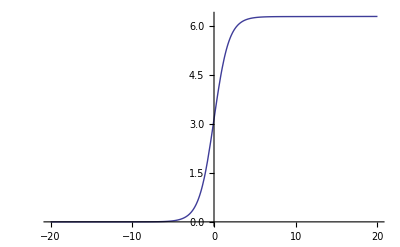

```mathematica
Plot[fun[x],{x,-20,20}]
```

```mathematica
eq1=eq1/.f0[x,t]->fun[x]
```

-ω^2 u[x]-((3-8 Cos[InterpolatingFunction[{{-13.0888,10.2248}},<>][x]]+Cos[2 InterpolatingFunction[{{-13.0888,10.2248}},<>][x]]) u[x])/(4 (2-Cos[InterpolatingFunction[{{-13.0888,10.2248}},<>][x]])^(3/2))-u''[x]==0

```mathematica
eqs=eq1/.ω^2->w2[x]
```

-((3-8 Cos[InterpolatingFunction[{{-13.0888,10.2248}},<>][x]]+Cos[2 InterpolatingFunction[{{-13.0888,10.2248}},<>][x]]) u[x])/(4 (2-Cos[InterpolatingFunction[{{-13.0888,10.2248}},<>][x]])^(3/2))-u[x] w2[x]-u''[x]==0

```mathematica
Clear[w2,u];sol=NDSolve[{eqs,D[w2[x],x]==0,u[-10]==0,u[10]==0,u'[-10]==0},{u,w2},x]
```

{{u→InterpolatingFunction[{{-10.,10.}},<>],w2→InterpolatingFunction[{{-10.,10.}},<>]}}

InterpolatingFunction[{{-10.,10.}},<>]

InterpolatingFunction[{{-10.,10.}},<>]

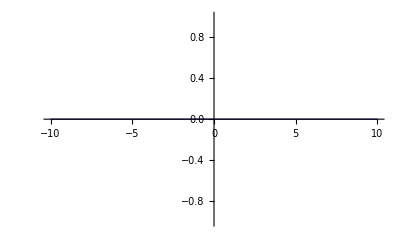

0.

```mathematica
w2=w2/.sol[[1]][[2]]
u=u/.sol[[1]][[1]]
Plot[u[x],{x,-10,10}]
w2[0]
```

```mathematica
eq2=(ω^2+(b^2 Cos[f0[x,t]+a*Sin[tau]])/(√(1+b^2-b^2 Cos[f0[x,t]+a*Sin[tau]]))-(b^4 Sin[f0[x,t]+a*Sin[tau]]^2)/(2 (1+b^2-b^2 Cos[f0[x,t]+a*Sin[tau]])^(3/2))) u[x]+u''[x]==0
```